# Straining Perovskite Unit Cells in All Crystallographic Directions

## Corey Teply WWU Master’s of Chemistry (September 2019 - August 2021) Dr. Robert Berger’s Computational Chemistry Lab

## Orthogonalize Functions

This section is our first approach to making perovskite unit cells strained in different directions. Although there are some useful functions in this section, this was not the method we ultimately used for making perovskite structures.

```mathematica
(*This function ensures that all basis vectors of a lattice are orthogonal*)
GramSchmidtInt[matrix_, int_]:=Module[
{numCol=Last[Dimensions[matrix]],i=2,j=1,k=1, m=1,orthoMatrixReals={},orthoMatrixInts,x1,x2={},x3={},tempVec,vecStar,uVec={}, transMat=Transpose[matrix],toreturn={}},
While[m≤numCol,
AppendTo[x2,0];
AppendTo[x3,0];
m=m+1];
vecStar=transMat⟦1⟧;
AppendTo[orthoMatrixReals, vecStar];
While[i≤numCol,
tempVec=transMat⟦i⟧;
While[j<i,
x1=Dot[tempVec,orthoMatrixReals⟦j⟧]/Dot[orthoMatrixReals⟦j⟧,orthoMatrixReals⟦j⟧];
AppendTo[uVec,x1];
j=j+1];
While[k≤i-1,
x2=x2+uVec⟦k⟧*orthoMatrixReals⟦k⟧;
k=k+1];
AppendTo[orthoMatrixReals,tempVec-x2];
x2=x3;
k=1;
j=1;
uVec={};
i=i+1];
If[int==0,(*if int is equal to 0, then return the rounded orthogonal basis*)
orthoMatrixInts=Transpose[orthoMatrixReals]; (*The last step rounds them to get them into integers*)
RoundEach[orthoMatrixInts],
orthoMatrixReals]](*if int≠0, then just return the orthogonal basis without rounding each element*)
```

```mathematica
(*The Hadamard Ratio computes if all the basis vectors of a lattice are reasonably orthogonal to each other, where a value of 1 denotes an orthogonal basis set*)
```

```mathematica
HadamardRatio[matrix_]:= Module[
{vectorProduct=1, det=Abs[Det[matrix]], n=Last[Dimensions[matrix]], k=1, ratio},
While[k≤n,
vectorProduct=vectorProduct* Norm[matrix⟦k⟧];
k=k+1];
ratio=(det/vectorProduct)^(1/n);
ratio]
```

```mathematica
OrthoMat[rho_,phi_,theta_]:=Module[{orthomat={},tempmat={},vec1={},vec2,vec3,r,x,y,z},
z=rho*Cos[phi*Pi/180];
r=rho*Sin[phi*Pi/180];
x=r*Cos[theta*Pi/180];
y=r*Sin[theta*Pi/180];
AppendTo[vec1,x];
AppendTo[vec1,y];
AppendTo[vec1,z];
vec2 = rho*Orthogonalize[{vec1,{0,r,0}}];
vec3 = rho*Orthogonalize[{vec1,{0,0,r}}];
AppendTo[tempmat,vec1];
AppendTo[tempmat,vec2⟦2⟧];
AppendTo[tempmat,vec3⟦2⟧];
GramSchmidtInt[Transpose[tempmat],1]]
```

```mathematica
MakeLeCubes[masterRho_,diffPhi_,diffTheta_]:=Module[{t=0,p=90,matList={},tempmat1, tempmat2={}},
While[t≤ 45,
While[p≥ 45,
tempmat1= OrthoMat[masterRho,p,t];
tempmat2 = SameLength[tempmat1,masterRho];
AppendTo[matList,tempmat2];
p=p-diffPhi];
t=t+diffTheta;
p=90];
matList]
```

```mathematica
AllOrtho[biglist_]:=Module[{count=0,x=0,y=0,z=0,k=1,badlist={}},
While[k≤ Length[biglist],
If[HadamardRatio[biglist⟦k⟧]== 1,
count=count+1,
AppendTo[badlist,k]];
k=k+1];
If[count==Length[biglist],
Print["all ortho"],
badlist]]
```

```mathematica
Pythag[vec_]:=Module[{},
Sqrt[vec⟦1⟧^2+vec⟦2⟧^2+vec⟦3⟧^2]]
```

```mathematica
AllGoodLength[biglist_,rho_]:=Module[{count=0,k=1,i=1,a=0,badlist={},tinyvec={}},
While[k≤ Length[biglist],
While[i≤ 3,
If[Norm[biglist⟦k,i⟧]== rho,
a=a+rho,
AppendTo[tinyvec,k];
AppendTo[tinyvec,i];
AppendTo[badlist,tinyvec];
tinyvec={}];
i=i+1];
If[a== 3*rho,
count=count+1];
k=k+1;
i=1;
a=0];
If[count== Length[biglist],
Print["all good length"],
badlist]]
```

```mathematica
SameLength[mat_,rho_]:=Module[{i=1,newmat={},scale, newvec={}},
While[i≤ 3,
scale= rho/Norm[mat⟦i⟧];
newvec=scale*mat⟦i⟧;
AppendTo[newmat,newvec];
i=i+1];
Transpose[newmat]]
```

```mathematica
TransposeAllCubes[zeList_]:=Module[{i=1, newList={},tempMat},
While[i<=Length[zeList],
tempMat = Transpose[zeList⟦i⟧];
AppendTo[newList,tempMat];
i=i+1;
];
newList]
```

```mathematica
FindAreas[diffTheta_, rho_]:=Module[{a=0,b=diffTheta,diffPhi,radA,radB,toReturn={},integral,area,denom,numIters,areaList={},angleList={},PT={},k=1,i=1,c=(Pi/4)*rho^2},
While[b≤ 90,
radA=DegtoRad[a];
radB=DegtoRad[b];
integral=Integrate[Sin[x],{x,radA,radB}];
area=integral*c;
AppendTo[areaList,area];
a=b;
b=b+diffTheta;
];
denom=areaList⟦1⟧;
While[k≤ Length[areaList],
If[k==1,
AppendTo[toReturn,Ceiling[areaList⟦k⟧/denom]],
AppendTo[toReturn,Ceiling[areaList⟦k⟧/denom*.5]]];
k=k+1;
];
k=1;
a=0;
b=0;
AppendTo[angleList,{0,0}];
While[k≤ Length[toReturn],
numIters=toReturn⟦k⟧;
b=diffTheta+b;
If[numIters== 1,
diffPhi=45/2,
diffPhi=45/numIters];
a=diffPhi;
AppendTo[angleList,{0,b}];
While[i≤ numIters,
AppendTo[PT,a];
AppendTo[PT,b];
AppendTo[angleList,PT];
a=diffPhi+a;
PT={};
i=i+1;
];
k=k+1;
i=1;
];
angleList]
```

## Choose Direction of Strain Functions

This section was the section used to rotate and strain perovskite unit cells.

```mathematica
(*RotateCube takes inputs of 
- rho: the length of one of the sides of a cubic perovskite unit cell
 - phi: the angle off of the z-axis
- theta: the angle off rotated in the x-y plane

From there, this function returns a cubic unit cell rotated by the angles given*)
```

```mathematica
RotateCube[rho_, phi_,theta_]:=Module[{ogMat = rho*IdentityMatrix[3],mat1={},mat2={}, vec={}},
(*First, pivot it about the x,y plane, so pivot it about the 3^rd column*)
(*first, find the first col vector*)
vec=RotateAboutZ[ogMat⟦1⟧,theta];
AppendTo[mat1,vec];
(*rotate second col vector*)
vec=RotateAboutZ[ogMat⟦2⟧,theta];
AppendTo[mat1,vec];
(*add the 3rd col vector, which doesn't need to be rotated for 5-atom perovskite unit cells*)
AppendTo[mat1,ogMat⟦3⟧];

(*now, incorperate the phi angle*)
vec=RotateAboutY[mat1⟦1⟧,phi];
AppendTo[mat2,vec];
vec = RotateAboutY[mat1⟦2⟧,phi];
AppendTo[mat2,vec];
vec=RotateAboutY[mat1⟦3⟧,phi];
AppendTo[mat2,vec];

Transpose[mat2]]
```

```mathematica
(*used for inputting an orginal matrix other than a unit cell length. Good for unit cells that aren't cubic, such as CsPbI3*)
```

```mathematica
RotateCube2[ogMat_, phi_,theta_]:=Module[{mat1={},Mat,mat2={}, vec={}},
(*First, pivot it about the x,y plane, so pivot it about the 3^rd column*)
(*first, find the first col vector*)
Mat=ogMat;
vec=RotateAboutZ[Mat⟦1⟧,theta];
AppendTo[mat1,vec];
(*rotate second col vector*)
vec=RotateAboutZ[Mat⟦2⟧,theta];
AppendTo[mat1,vec];
vec=RotateAboutZ[Mat⟦3⟧,theta];
AppendTo[mat1,vec];

(*now, incorperate the phi angle*)
vec=RotateAboutY[mat1⟦1⟧,phi];
AppendTo[mat2,vec];
vec = RotateAboutY[mat1⟦2⟧,phi];
AppendTo[mat2,vec];
vec=RotateAboutY[mat1⟦3⟧,phi];
AppendTo[mat2,vec];

Transpose[mat2]]
```

```mathematica
(*This returns the angles that each of the unit cells were rotated. It's good to use after rotating the unit cells to check and make sure everything ran smoothly.*)
```

```mathematica
ReturnAngles[list_,rho_]:=Module[{toReturn={}, theta,phi,k=1,len=Length[list],mat0, mat1={},mat2={},angleList={},vec},
While[k≤ len,
mat0=list⟦k⟧;

(*find phi first*)
phi=RadtoDeg[ArcCos[mat0⟦3,3⟧/Norm[mat0⟦3⟧]]];
AppendTo[angleList,phi];
vec=RotateAboutY[mat0⟦1⟧,360-phi];
AppendTo[mat1,vec];
vec = RotateAboutY[mat0⟦2⟧,360-phi];
AppendTo[mat1,vec];
vec = RotateAboutY[mat0⟦3⟧,360-phi];
AppendTo[mat1,vec];

(*next, find theta*)
theta=RadtoDeg[ArcTan[mat1⟦1,2⟧/mat1⟦1,1⟧]];
AppendTo[angleList,theta];
vec=RotateAboutZ[mat1⟦1⟧,360-theta];
AppendTo[mat2,vec];
vec=RotateAboutZ[mat1⟦2⟧,360-theta];
AppendTo[mat2,vec];
AppendTo[mat2,mat1⟦3⟧];

AppendTo[toReturn,angleList];
mat1={};
mat2={};
angleList={};
k=k+1;
];
toReturn]
```

```mathematica
(*All rotations are clockwise rotations*)
```

```mathematica
RotateAboutX[vec_,deg_]:=Module[{rotationMat={},tempVec={},toReturn},
(*first row*)
AppendTo[rotationMat,{1,0,0}];
(*second row*)
AppendTo[tempVec,0];
AppendTo[tempVec, Cos[deg*Pi/180]];
AppendTo[tempVec,-1*Sin[deg*Pi/180]];
AppendTo[rotationMat,tempVec];
tempVec = {};
(*third row*)
AppendTo[tempVec,0];
AppendTo[tempVec,Sin[deg*Pi/180]];
AppendTo[tempVec,Cos[deg*Pi/180]];
AppendTo[rotationMat,tempVec];
(*perform rotation*)
toReturn = rotationMat.vec;
toReturn
]
```

```mathematica
RotateAboutY[vec_,deg_]:=Module[{rotationMat={},tempVec={},toReturn},
(*first row*)
AppendTo[tempVec,Cos[deg*Pi/180]];
AppendTo[tempVec,0];
AppendTo[tempVec,Sin[deg*Pi/180]];
AppendTo[rotationMat,tempVec];
tempVec={};
(*second row*)
AppendTo[rotationMat,{0,1,0}];
(*thrid row*)
AppendTo[tempVec,-1*Sin[deg*Pi/180]];
AppendTo[tempVec,0];
AppendTo[tempVec,Cos[deg*Pi/180]];
AppendTo[rotationMat,tempVec];
(*perform rotation*)
toReturn=rotationMat.vec;
toReturn
]
```

```mathematica
RotateAboutZ[vec_,deg_]:=Module[{rotationMat={},tempVec={},toReturn},
(*first row*)
AppendTo[tempVec,Cos[deg*Pi/180]];
AppendTo[tempVec,-1*Sin[deg*Pi/180]];
AppendTo[tempVec,0];
AppendTo[rotationMat,tempVec];
tempVec={};
(*second row*)
AppendTo[tempVec,Sin[deg*Pi/180]];
AppendTo[tempVec,Cos[deg*Pi/180]];
AppendTo[tempVec,0];
AppendTo[rotationMat,tempVec];
(*third row*)
AppendTo[rotationMat,{0,0,1}];
(*perform rotation*)
toReturn=rotationMat.vec;
toReturn
]
```

```mathematica
RadtoDeg[rad_]:=Module[{},
rad*180/Pi]
```

```mathematica
DegtoRad[deg_]:=Module[{},
deg*Pi/180]
```

```mathematica
RandomTheta[upperBound_]:=Module[{},
RandomReal[{0,upperBound}]]
```

```mathematica
RandomPhi[upperBound_]:=Module[{ub},
ub=Sin[DegtoRad[upperBound]];
RadtoDeg[ArcCos[RandomReal[{0,ub}]]]]
```

```mathematica
(*Strain 2 out of the 3 axes of the unit cell to emulate the concept of biaxial strain*)
```

```mathematica
AddStrain[mat_,c_]:=Module[{newMat={}, x, y, z,xList={},yList={},zList={},i=1},
x=c*mat⟦1⟧;
AppendTo[newMat,x];
y=c*mat⟦2⟧;
AppendTo[newMat,y];
z=mat⟦3⟧;
AppendTo[newMat,z];
Transpose[newMat]]
```

```mathematica
RandomCubes[numCubes_, masterRho_, diffTheta_,diffPhi_,strain_]:=Module[{i=1,biglist={},p,t,tempMat1,tempMat2},
While[i<=numCubes,
p=RandomPhi[diffPhi];
t=RandomTheta[diffTheta];
tempMat1 = RotateCube[masterRho,p,t];
tempMat2 = AddStrain[tempMat1,strain];
AppendTo[biglist,tempMat2];
i=i+1];
biglist]
```

```mathematica
DistributedCubes[strainList_, masterRho_, strain_]:=Module[{i=1,biglist={},p,t,tempMat1,tempMat2},
While[i≤Length[strainList],
p=strainList⟦i,2⟧;
t=strainList⟦i,1⟧;
tempMat1 = RotateCube[masterRho,p,t];
tempMat2 = AddStrain[tempMat1,strain];
AppendTo[biglist,tempMat2];
i=i+1];
biglist]
```

```mathematica
(*for cubic unit cells*)
```

```mathematica
DistributedCubes2[strainList_, masterRho_, strain_]:=Module[{i=1,biglist={},p,t,ang={},allAngles={},sphericals,tempMat1,tempMat2},
AppendTo[biglist,AddStrain[masterRho*IdentityMatrix[3],strain]];
While[i≤Length[strainList],
sphericals=RadtoDeg[CoordinateTransformData["Cartesian"->"Spherical","Mapping",strainList⟦i⟧]];
p=sphericals⟦2⟧;
t=sphericals⟦3⟧;
AppendTo[ang,p];
AppendTo[ang,t];
AppendTo[allAngles,ang];
ang={};
tempMat1 = RotateCube[masterRho,p,t];
tempMat2 = AddStrain[tempMat1,strain];
AppendTo[biglist,tempMat2];
i=i+1];
biglist]
```

```mathematica
(*for inputting an orginal matrix instead of a unit cell length. Good for unit cells that aren't cubic*)
```

```mathematica
DistributedCubes3[strainList_, ogMat_, strain_]:=Module[{i=1,biglist={},p,t,ang={},allAngles={},sphericals,tempMat1,tempMat2},
AppendTo[biglist,AddStrain[Transpose[ogMat],strain]];
While[i≤Length[strainList],
sphericals=RadtoDeg[CoordinateTransformData["Cartesian"->"Spherical","Mapping",strainList⟦i⟧]];
p=sphericals⟦2⟧;
t=sphericals⟦3⟧;
AppendTo[ang,p];
AppendTo[ang,t];
AppendTo[allAngles,ang];
ang={};
tempMat1 = RotateCube2[ogMat,p,t];
tempMat2 = AddStrain[tempMat1,strain];
AppendTo[biglist,tempMat2];
i=i+1];
biglist]
```

## Heat Map Functions/Lists

This section has all of the code that was used to make heat maps for the band gaps and angles of distortion.

```mathematica
AddRadius[list_,rho_]:=Module[{bigList={},k=2,tempList={}},
While[k≤ Length[list],
AppendTo[tempList,rho];
AppendTo[tempList,DegtoRad[list⟦k,1⟧]];
AppendTo[tempList,DegtoRad[list⟦k,2⟧]];
AppendTo[bigList,tempList];
tempList={};
k=k+1];
bigList]
```

```mathematica
CompileHeatMap[bgList_,angleList_]:=Module[{toReturn={},k=1,tempCoords={}},
AppendTo[tempCoords,0];
AppendTo[tempCoords,0];
AppendTo[tempCoords,bgList⟦1⟧];
AppendTo[toReturn,tempCoords];
tempCoords={};
While[k≤ Length[angleList],
AppendTo[tempCoords,angleList⟦k,1⟧];
AppendTo[tempCoords,angleList⟦k,2⟧];
AppendTo[tempCoords, bgList⟦k+1⟧];
AppendTo[toReturn,tempCoords];
tempCoords={};
k=k+1;
];
toReturn]
```

```mathematica
MakeListPlot[list_,index_]:=Module[{toReturn={},k=1},
While[k≤ Length[list],
AppendTo[toReturn,list⟦k,index⟧];
k=k+1];
toReturn]
```

```mathematica
MakeTable[bgList_]:=Module[{masterList={},row1={},k=1},
AppendTo[row1,"x"];
AppendTo[row1,"y"];
AppendTo[row1,"BGs"];
AppendTo[masterList,row1];
While[k≤Length[bgList],
AppendTo[masterList,bgList⟦k⟧];
k=k+1];
masterList]
```

```mathematica
CartesianVecs:={{.25,0,1},{.5,0,1},{.75,0,1},{1,0,1},{.25,.25,1},{.5,.25,1},{.75,.25,1},{1,.25,1},{.5,.5,1},{.75,.5,1},{1,.5,1},{.75,.75,1},{1,.75,1},{1,1,1}}
```

```mathematica
CartesianVecsNEW:={{0,0,1},{.25,0,1},{.5,0,1},{.75,0,1},{1,0,1},{.25,.25,1},{.5,.25,1},{.75,.25,1},{1,.25,1},{.5,.5,1},{.75,.5,1},{1,.5,1},{.75,.75,1},{1,.75,1},{1,1,1}}
```

```mathematica
CartesianVecs2:={{-1,-1,1},{-.5,-1,1},{0,-1,1},{.5,-1,1},{1,-1,1},
{-1,-.5,1},{-.5,-.5,1},{0,-.5,1},{.5,-.5,1},{1,-.5,1},
{-1,0,1},{-.5,0,1},(*0,0,0*){.5,0,1},{1,0,1},
{-1,.5,1},{-.5,.5,1},{0,.5,1},{.5,.5,1},{1,.5,1},
{-1,1,1},{-.5,1,1},{0,1,1},{.5,1,1},{1,1,1},
{-1,-1,.5},{-.5,-1,.5},{0,-1,.5},{.5,-1,.5},{1,-1,.5},
{1,-.5,.5},{1,0,.5},{1,.5,.5},
{-1,-.5,.5},{-1,0,.5},{-1,.5,.5},
{-1,1,.5},{-.5,1,.5},{0,1,.5},{.5,1,.5},{1,1,.5},
{-1,-1,0},{-.5,-1,0},{0,-1,0},{.5,-1,0},{1,-1,0},
{1,-.5,.0},{1,0,0},{1,.5,0},
{-1,-.5,0},{-1,0,0},{-1,.5,0},
{-1,1,0},{-.5,1,0},{0,1,0},{.5,1,0},{1,1,0}}
```

```mathematica
CartesianVecs3:={{-1,-1,1},{-.5,-1,1},{0,-1,1},{.5,-1,1},{1,-1,1},
{-1,-.5,1},{-.5,-.5,1},{0,-.5,1},{.5,-.5,1},{1,-.5,1},
{-1,0,1},{-.5,0,1},(*0,0,0*)
{-1,.5,1},{-.5,.5,1},{0,.5,1},
{-1,1,1},{-.5,1,1},{0,1,1},{.5,1,1},
{-1,-1,.5},{-.5,-1,.5},{0,-1,.5},{.5,-1,.5},{1,-1,.5},
{1,-.5,.5},{1,0,.5},{1,.5,.5},
{-1,-.5,.5},{-1,0,.5},{-1,.5,.5},
{-1,1,.5},{-.5,1,.5},{0,1,.5},{.5,1,.5},{1,1,.5},
{-1,-1,0},{-.5,-1,0},{0,-1,0},{.5,-1,0},{1,-1,0},
{1,-.5,.0},{1,0,0},{1,.5,0},
{-1,-.5,0},{-1,0,0},{-1,.5,0},
{-1,1,0},{-.5,1,0},{0,1,0},{.5,1,0},{1,1,0}}
```

```mathematica
CartesianVecs4 := {{.5,0,1},{1,0,1},{.5,.5,1},{1,.5,1},{1,1,1}}
```

```mathematica
ze15Angles:={{0,0},{14.036243467926479,0.},{26.56505117707799,0.},{36.86989764584402,0.},{45.,0.},{19.471220634490695,45.},{29.20593224739942,26.56505117707799},{38.32881810145589,18.43494882292201},{45.868250787968954,14.036243467926479},{35.264389682754654,45.},{42.03111377419729,33.690067525979785},{48.189685104221404,26.56505117707799},{46.68614334171695,45.},{51.34019174590991,36.86989764584402},{54.735610317245346,45.}}
```

```mathematica
barLengendList :=Range[0,24,1]
```

```mathematica
ColorWheel[x_,range_]:=ColorData["Rainbow"][1-Rescale[x,range]]
```

```mathematica
barAxisLabels := Directive[FontSize-> 16,Black]
```

```mathematica
findMinVal[finalList_]:=Module[
{minVal=90,disMin,k=1},
While[k≤ Length[finalList],
disMin=finalList⟦k,3⟧;
If[disMin<minVal,
minVal=disMin];
k=k+1;
];
minVal]
```

```mathematica
SphericalCoords=AddRadius[ze15Angles,UnitCellLength]
```

{{5.61158,0.244979,0.},{5.61158,0.463648,0.},{5.61158,0.643501,0.},{5.61158,0.785398,0.},{5.61158,0.339837,0.785398},{5.61158,0.50974,0.463648},{5.61158,0.668964,0.321751},{5.61158,0.800552,0.244979},{5.61158,0.61548,0.785398},{5.61158,0.733581,0.588003},{5.61158,0.841069,0.463648},{5.61158,0.814827,0.785398},{5.61158,0.896055,0.643501},{5.61158,0.955317,0.785398}}

```mathematica
Show[SphericalPlot3D[UnitCellLength-.05,{θ,0,Pi},{ϕ,0,2*Pi}],
Graphics3D@{Point[CoordinateTransformData["Spherical"-> "Cartesian","Mapping",#] & /@ SphericalCoords]},Boxed->False]
```

-Graphics3D-

## CsPbI3 Compounds

The CsPbI3 compounds rotated and compressively strained.

```mathematica
CsPbI3Poscar1:={{-6.3957611110, 6.3957611110, 0.0000000000},
{0.0000000000, 0.0000000000, 12.7915222200},
{6.3957611110, 6.3957611110, 0.0000000000}}
```

```mathematica
poscar1=DistributedCubes3[CartesianVecs,CsPbI3Poscar1,.98]
```

{{{-6.26785,6.26785,0.},{0.,0.,12.7915},{6.26785,6.26785,0.}},{{-6.0807,6.26785,1.5512},{3.04035,0.,12.4096},{6.0807,6.26785,-1.5512}},{{-5.60613,6.26785,2.86027},{5.60613,0.,11.4411},{5.60613,6.26785,-2.86027}},{{-5.01428,6.26785,3.83746},{7.52142,0.,10.2332},{5.01428,6.26785,-3.83746}},{{-4.43204,6.26785,4.52249},{8.86407,0.,9.04497},{4.43204,6.26785,-4.52249}},{{-8.35713,0.,3.01499},{4.17856,0.,12.06},{0.,8.86407,0.}},{{-7.34015,2.80307,4.18701},{6.11679,0.,11.1654},{2.44672,8.4092,-1.39567}},{{-6.21944,3.96413,5.01725},{7.77431,0.,10.0345},{3.10972,7.92827,-2.50862}},{{-5.29257,4.56053,5.5668},{8.99737,0.,8.90687},{3.17554,7.60088,-3.34008}},{{-7.23749,0.,5.22212},{7.23749,0.,10.4442},{0.,8.86407,0.}},{{-6.45621,1.73839,5.93832},{8.39307,0.,9.5013},{1.29124,8.69194,-1.18766}},{{-5.60613,2.80307,6.39576},{9.34355,0.,8.52768},{1.86871,8.4092,-2.13192}},{{-6.0807,0.,6.58118},{9.12106,0.,8.77491},{0.,8.86407,0.}},{{-5.48169,1.25357,6.99195},{9.78873,0.,7.9908},{0.783098,8.77498,-0.99885}},{{-5.11767,0.,7.38519},{10.2353,0.,7.38519},{0.,8.86407,0.}}}

```mathematica
poscar1b=DistributedCubes3[CartesianVecs4,CsPbI3Poscar1,.98]
```

{{{-6.26785,6.26785,0.},{0.,0.,12.7915},{6.26785,6.26785,0.}},{{-5.60613,6.26785,2.86027},{5.60613,0.,11.4411},{5.60613,6.26785,-2.86027}},{{-4.43204,6.26785,4.52249},{8.86407,0.,9.04497},{4.43204,6.26785,-4.52249}},{{-7.23749,0.,5.22212},{7.23749,0.,10.4442},{0.,8.86407,0.}},{{-5.60613,2.80307,6.39576},{9.34355,0.,8.52768},{1.86871,8.4092,-2.13192}},{{-5.11767,0.,7.38519},{10.2353,0.,7.38519},{0.,8.86407,0.}}}

```mathematica
CsPbI3Poscar2:={{6.3957611110, 6.3957611110, 0.0000000000},
{0.0000000000, 0.0000000000, 12.7915222200},
{6.3957611110, -6.3957611110, 0.0000000000}}
```

```mathematica
poscar2=DistributedCubes3[CartesianVecs, CsPbI3Poscar2,.98]
```

{{{6.26785,6.26785,0.},{0.,0.,12.7915},{6.26785,-6.26785,0.}},{{6.0807,6.26785,-1.5512},{3.04035,0.,12.4096},{6.0807,-6.26785,-1.5512}},{{5.60613,6.26785,-2.86027},{5.60613,0.,11.4411},{5.60613,-6.26785,-2.86027}},{{5.01428,6.26785,-3.83746},{7.52142,0.,10.2332},{5.01428,-6.26785,-3.83746}},{{4.43204,6.26785,-4.52249},{8.86407,0.,9.04497},{4.43204,-6.26785,-4.52249}},{{0.,8.86407,0.},{4.17856,0.,12.06},{8.35713,0.,-3.01499}},{{2.44672,8.4092,-1.39567},{6.11679,0.,11.1654},{7.34015,-2.80307,-4.18701}},{{3.10972,7.92827,-2.50862},{7.77431,0.,10.0345},{6.21944,-3.96413,-5.01725}},{{3.17554,7.60088,-3.34008},{8.99737,0.,8.90687},{5.29257,-4.56053,-5.5668}},{{0.,8.86407,0.},{7.23749,0.,10.4442},{7.23749,0.,-5.22212}},{{1.29124,8.69194,-1.18766},{8.39307,0.,9.5013},{6.45621,-1.73839,-5.93832}},{{1.86871,8.4092,-2.13192},{9.34355,0.,8.52768},{5.60613,-2.80307,-6.39576}},{{0.,8.86407,0.},{9.12106,0.,8.77491},{6.0807,0.,-6.58118}},{{0.783098,8.77498,-0.99885},{9.78873,0.,7.9908},{5.48169,-1.25357,-6.99195}},{{0.,8.86407,0.},{10.2353,0.,7.38519},{5.11767,0.,-7.38519}}}

```mathematica
CsPbI3Poscar3:={{6.3957611110,0, 6.3957611110},
{0.0000000000, 12.7915222200,0},
{-6.3957611110, 0, 6.3957611110}}
```

```mathematica
poscar3=DistributedCubes3[CartesianVecs, CsPbI3Poscar3,.98]
```

{{{6.26785,0.,6.39576},{0.,12.5357,0},{-6.26785,0.,6.39576}},{{7.60088,0.,4.6536},{0.,12.5357,0.},{-4.56053,0.,7.756}},{{8.4092,0.,2.86027},{0.,12.5357,0.},{-2.80307,0.,8.58081}},{{8.77498,0.,1.27915},{0.,12.5357,0.},{-1.25357,0.,8.95407}},{{8.86407,0.,0.},{0.,12.5357,0.},{0.,0.,9.04497}},{{6.26785,4.43204,4.52249},{-8.35713,8.86407,3.01499},{-2.08928,-4.43204,7.53748}},{{7.95183,2.80307,2.79134},{-4.89343,11.2123,2.79134},{-1.83504,-2.80307,8.37402}},{{8.55174,1.98207,1.25431},{-3.10972,11.8924,2.50862},{-0.777431,-1.98207,8.78018}},{{8.73275,1.52018,8.88178×10^-16},{-2.11703,12.1614,2.22672},{0.264629,-1.52018,8.90687}},{{7.23749,4.43204,2.61106},{-7.23749,8.86407,5.22212},{4.35207×10^-16,-4.43204,7.83318}},{{8.07026,3.47678,1.18766},{-5.16497,10.4303,4.75065},{0.32281,-3.47678,8.31364}},{{8.4092,2.80307,0.},{-3.73742,11.2123,4.26384},{0.934355,-2.80307,8.52768}},{{7.60088,4.43204,1.09686},{-6.0807,8.86407,6.58118},{1.52018,-4.43204,7.67805}},{{8.02676,3.76071,-1.33227×10^-15},{-4.69859,10.0286,5.9931},{1.76197,-3.76071,7.9908}},{{7.67651,4.43204,4.44089×10^-16},{-5.11767,8.86407,7.38519},{2.55884,-4.43204,7.38519}}}

```mathematica
CsPbI3Poscar4:={{6.3957611110,0, -6.3957611110},
{0.0000000000, 12.7915222200,0},
{6.3957611110, 0, 6.3957611110}}
```

```mathematica
poscar4=DistributedCubes3[CartesianVecs,CsPbI3Poscar4,.98]
```

{{{6.26785,0.,-6.39576},{0.,12.5357,0},{6.26785,0.,6.39576}},{{4.56053,0.,-7.756},{0.,12.5357,0.},{7.60088,0.,4.6536}},{{2.80307,0.,-8.58081},{0.,12.5357,0.},{8.4092,0.,2.86027}},{{1.25357,0.,-8.95407},{0.,12.5357,0.},{8.77498,0.,1.27915}},{{0.,0.,-9.04497},{0.,12.5357,0.},{8.86407,0.,0.}},{{2.08928,4.43204,-7.53748},{-8.35713,8.86407,3.01499},{6.26785,4.43204,4.52249}},{{1.83504,2.80307,-8.37402},{-4.89343,11.2123,2.79134},{7.95183,2.80307,2.79134}},{{0.777431,1.98207,-8.78018},{-3.10972,11.8924,2.50862},{8.55174,1.98207,1.25431}},{{-0.264629,1.52018,-8.90687},{-2.11703,12.1614,2.22672},{8.73275,1.52018,8.88178×10^-16}},{{-4.35207×10^-16,4.43204,-7.83318},{-7.23749,8.86407,5.22212},{7.23749,4.43204,2.61106}},{{-0.32281,3.47678,-8.31364},{-5.16497,10.4303,4.75065},{8.07026,3.47678,1.18766}},{{-0.934355,2.80307,-8.52768},{-3.73742,11.2123,4.26384},{8.4092,2.80307,0.}},{{-1.52018,4.43204,-7.67805},{-6.0807,8.86407,6.58118},{7.60088,4.43204,1.09686}},{{-1.76197,3.76071,-7.9908},{-4.69859,10.0286,5.9931},{8.02676,3.76071,-1.33227×10^-15}},{{-2.55884,4.43204,-7.38519},{-5.11767,8.86407,7.38519},{7.67651,4.43204,4.44089×10^-16}}}

```mathematica
CsPbI3Poscar5:={{0,-6.3957611110, 6.3957611110},
{12.7915222200,0,0},
{0,6.3957611110, 6.3957611110}}
```

```mathematica
poscar5=DistributedCubes3[CartesianVecs,CsPbI3Poscar5,.98]
```

{{{0.,-6.26785,6.39576},{12.5357,0.,0},{0.,6.26785,6.39576}},{{1.52018,-6.26785,6.2048},{12.1614,0.,-3.1024},{1.52018,6.26785,6.2048}},{{2.80307,-6.26785,5.72054},{11.2123,0.,-5.72054},{2.80307,6.26785,5.72054}},{{3.76071,-6.26785,5.11661},{10.0286,0.,-7.67491},{3.76071,6.26785,5.11661}},{{4.43204,-6.26785,4.52249},{8.86407,0.,-9.04497},{4.43204,6.26785,4.52249}},{{6.26785,-4.43204,4.52249},{8.35713,8.86407,-3.01499},{-2.08928,4.43204,7.53748}},{{5.50511,-5.60613,4.18701},{9.78687,5.60613,-5.58268},{0.611679,5.60613,6.97835}},{{5.44201,-5.9462,3.76294},{9.32917,3.96413,-7.52587},{2.33229,5.9462,6.27156}},{{5.5572,-6.0807,3.34008},{8.46812,3.04035,-8.90687},{3.44017,6.0807,5.5668}},{{7.23749,-4.43204,2.61106},{7.23749,8.86407,-5.22212},{4.35207×10^-16,4.43204,7.83318}},{{6.77902,-5.21516,2.37533},{7.74745,6.95355,-7.12598},{1.61405,5.21516,7.12598}},{{6.54049,-5.60613,2.13192},{7.47484,5.60613,-8.52768},{2.80307,5.60613,6.39576}},{{7.60088,-4.43204,1.09686},{6.0807,8.86407,-6.58118},{1.52018,4.43204,7.67805}},{{7.24366,-5.01428,0.99885},{6.26479,7.52142,-7.9908},{2.54507,5.01428,6.99195}},{{7.67651,-4.43204,4.44089×10^-16},{5.11767,8.86407,-7.38519},{2.55884,4.43204,7.38519}}}

```mathematica
CsPbI3Poscar6:={{0,6.3957611110, 6.3957611110},
{12.7915222200,0,0},
{0,6.3957611110, -6.3957611110}}
```

```mathematica
poscar6=DistributedCubes3[CartesianVecs,CsPbI3Poscar6,.98]
```

{{{0.,6.26785,6.39576},{12.5357,0.,0},{0.,6.26785,-6.39576}},{{1.52018,6.26785,6.2048},{12.1614,0.,-3.1024},{-1.52018,6.26785,-6.2048}},{{2.80307,6.26785,5.72054},{11.2123,0.,-5.72054},{-2.80307,6.26785,-5.72054}},{{3.76071,6.26785,5.11661},{10.0286,0.,-7.67491},{-3.76071,6.26785,-5.11661}},{{4.43204,6.26785,4.52249},{8.86407,0.,-9.04497},{-4.43204,6.26785,-4.52249}},{{-2.08928,4.43204,7.53748},{8.35713,8.86407,-3.01499},{-6.26785,4.43204,-4.52249}},{{0.611679,5.60613,6.97835},{9.78687,5.60613,-5.58268},{-5.50511,5.60613,-4.18701}},{{2.33229,5.9462,6.27156},{9.32917,3.96413,-7.52587},{-5.44201,5.9462,-3.76294}},{{3.44017,6.0807,5.5668},{8.46812,3.04035,-8.90687},{-5.5572,6.0807,-3.34008}},{{4.35207×10^-16,4.43204,7.83318},{7.23749,8.86407,-5.22212},{-7.23749,4.43204,-2.61106}},{{1.61405,5.21516,7.12598},{7.74745,6.95355,-7.12598},{-6.77902,5.21516,-2.37533}},{{2.80307,5.60613,6.39576},{7.47484,5.60613,-8.52768},{-6.54049,5.60613,-2.13192}},{{1.52018,4.43204,7.67805},{6.0807,8.86407,-6.58118},{-7.60088,4.43204,-1.09686}},{{2.54507,5.01428,6.99195},{6.26479,7.52142,-7.9908},{-7.24366,5.01428,-0.99885}},{{2.55884,4.43204,7.38519},{5.11767,8.86407,-7.38519},{-7.67651,4.43204,-4.44089×10^-16}}}

## Rotate Cube in terms of direction of strain

This section actually deals with rotating and straining the perovskite unit cells in all crystallographic directions.

Step 1: Define the unit cell length (in Angstroms) of your fully relaxed, cubic perovskite structure.

```mathematica
UnitCellLength = 5.6115828017740581
```

5.61158

Step 2: Run it through DistributedCubes2 to strain it in all directions. The parameters are [{Cartesian coordinates of the axis perpendicular to the plane of biaxial strain}, UnitCellLenth, the amount of strain to be applied (0.98 = -2% compressive strain)]

```mathematica
MathlierCubes=DistributedCubes2[CartesianBois,UnitCellLength,0.98]//N
```

{{{5.49935,0.,0.},{0.,5.49935,0.},{0.,0.,5.61158}},{{5.33515,0.,-1.36101},{0.,5.49935,0.},{1.33379,0.,5.44403}},{{4.91877,0.,-2.50958},{0.,5.49935,0.},{2.45938,0.,5.01915}},{{4.39948,0.,-3.36695},{0.,5.49935,0.},{3.29961,0.,4.48927}},{{3.88863,0.,-3.96799},{0.,5.49935,0.},{3.88863,0.,3.96799}},{{3.66623,3.88863,-1.32266},{-3.66623,3.88863,1.32266},{1.83312,0.,5.29065}},{{4.29345,2.45938,-2.4491},{-2.14673,4.91877,1.22455},{2.68341,0.,4.89819}},{{4.09266,1.73905,-3.30157},{-1.36422,5.21714,1.10052},{3.41055,0.,4.40209}},{{3.71492,1.33379,-3.9074},{-0.928731,5.33515,0.976851},{3.94711,0.,3.9074}},{{3.17505,3.88863,-2.29092},{-3.17505,3.88863,2.29092},{3.17505,0.,4.58184}},{{3.39877,3.05049,-3.12613},{-2.26585,4.57574,2.08409},{3.682,0.,4.16818}},{{3.27918,2.45938,-3.74106},{-1.63959,4.91877,1.87053},{4.09897,0.,3.74106}},{{2.66758,3.88863,-2.88714},{-2.66758,3.88863,2.88714},{4.00137,0.,3.84951}},{{2.74833,3.29961,-3.50553},{-2.06125,4.39948,2.62915},{4.29427,0.,3.50553}},{{2.2451,3.88863,-3.23985},{-2.2451,3.88863,3.23985},{4.4902,0.,3.23985}}}

Step 3: Copy this output to a .txt file and run through the .java code in the “GeneratePOSCARs” repo on my GitHub page. Instructions on how to do that can be found in the readME file in that repo.

## Make Heat Map

This section allows you to make heat maps of the computed band gaps from running VASP calculations.

Step 1: Input the band gaps in the order of calculations found in “CartesianVecs” and make a list of the band gaps.

```mathematica
ze15BGs:={1.2533,1.3305,1.4478,1.4594,1.4881,1.361,1.4694,1.499,1.5159,1.527,1.546,1.5602,1.567,1.577,1.5678}
```

Step 2: Input that band gap list into the CompileHeatMap function, which pairs the band gap to the corresponding axis perpendicular to the plane of strain

```mathematica
fuego=CompileHeatMap[ze15BGs,CartesianVecs]
```

{{0,0,1.2533},{0.25,0,1.3305},{0.5,0,1.4478},{0.75,0,1.4594},{1,0,1.4881},{0.25,0.25,1.361},{0.5,0.25,1.4694},{0.75,0.25,1.499},{1,0.25,1.5159},{0.5,0.5,1.527},{0.75,0.5,1.546},{1,0.5,1.5602},{0.75,0.75,1.567},{1,0.75,1.577},{1,1,1.5678}}

Step 3: Plot the band gaps (or angles of ferroelectric distortion) using the ListDensityPlot code below.

```mathematica
(*for angles of b-site distortion*)
```

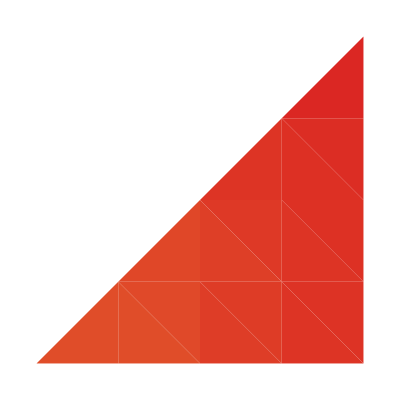

```mathematica
ListDensityPlot[fuego,PlotLegends->BarLegend[
{(ColorWheel[#,{0,Max[Ceiling[fuego]]}]&/@ Range[0,Max[Ceiling[fuego]],.1]),{0,90}},
LegendLabel->"Angle off Axis (in degrees)",
LegendFunction->(Framed[#1, RoundingRadius -> 5] & ),
LabelStyle->{FontSize->12,FontName-> "Arial",Black}
],PlotRange->All,ColorFunction->(ColorWheel[#,{0,90}]&/@Range[findMinVal[fuego],Max[Ceiling[fuego]],.1]),Frame->False]
```

```mathematica
(*for band gap heat maps*)
```

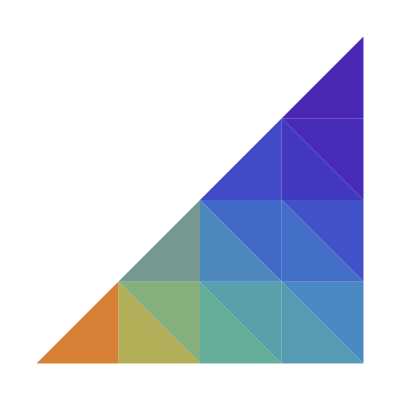

```mathematica
ListDensityPlot[fuego,PlotLegends->BarLegend[
{(ColorWheel[#,{1.25,Max[fuego]}]&/@ Range[1.25,Max[fuego],.0005]),{1.25,1.6}},
LegendLabel->"Band Gap (eV)",
LegendFunction->(Framed[#1, RoundingRadius -> 5] & ),
LabelStyle->{FontSize->12,FontName-> "Arial",Black}
],PlotRange->All,ColorFunction->(ColorWheel[#,{1.25,1.6}]&/@Range[findMinVal[fuego],Max[fuego],.0005]),Frame->False]
```